```mathematica
g1[k1_,k2_,k3_]:=Cos[π/2 k1]Cos[π/2 k2]Cos[π/2 k3]-I Sin[π/2 k1]Sin[π/2 k2]Sin[π/2 k3];
g2[k1_,k2_,k3_]:=-Cos[π/2 k1]Sin[π/2 k2]Sin[π/2 k3]+I Sin[π/2 k1]Cos[π/2 k2]Cos[π/2 k3];
g3[k1_,k2_,k3_]:=-Sin[π/2 k1]Cos[π/2 k2]Sin[π/2 k3]+I Cos[π/2 k1]Sin[π/2 k2]Cos[π/2 k3];
g4[k1_,k2_,k3_]:=-Sin[π/2 k1]Sin[π/2 k2]Cos[π/2 k3]+I Cos[π/2 k1]Cos[π/2 k2]Sin[π/2 k3];
```

```mathematica
spMatrix={
{Es1,0,0,0,Vss g1[k1,k2,k3],Vs1p g2[k1,k2,k3],Vs1p g3[k1,k2,k3],Vs1p g4[k1,k2,k3]},
{0,Ep1,0,0,-Vs2p g2[k1,k2,k3],Vxx g1[k1,k2,k3],Vxy g4[k1,k2,k3],Vxy g3[k1,k2,k3]},
{0,0,Ep1,0,-Vs2p g3[k1,k2,k3],Vxy g4[k1,k2,k3], Vxx g1[k1,k2,k3], Vxy g2[k1,k2,k3]},
{0,0,0,Ep1,-Vs2p g4[k1,k2,k3],Vxy g3[k1,k2,k3],Vxy g2[k1,k2,k3],Vxx g1[k1,k2,k3]},
{Vss g1[k1,k2,k3]*,-Vs2p g2[k1,k2,k3]*,-Vs2p g3[k1,k2,k3]*,-Vs2p g4[k1,k2,k3]*,Es2,0,0,0},
{Vs1p g2[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,Vxy g4[k1,k2,k3]*,Vxy g3[k1,k2,k3]*,0,Ep2,0,0},
{Vs1p g3[k1,k2,k3]*,Vxy g4[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,Vxy g2[k1,k2,k3]*,0,0,Ep2,0},
{Vs1p g4[k1,k2,k3]*,Vxy g3[k1,k2,k3]*,Vxy g2[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,0,0,0,Ep2}
};
```

```mathematica
(*GaAs*)
(*Es1=-6.01;
Ep1=0.19;
Es2=-4.79;
Ep2=4.59;
Vss=-7.00;
Vs1p=7.28;
Vs2p=3.70;
Vxx=0.93;
Vxy=4.72;*)

(*ZnSe*)
Es1=-8.92;
Ep1=0.12;
Es2=-0.28;
Ep2=7.42;
Vss=-6.14;
Vs1p=5.47;
Vs2p=4.73;
Vxx=0.96;
Vxy=4.38;
```

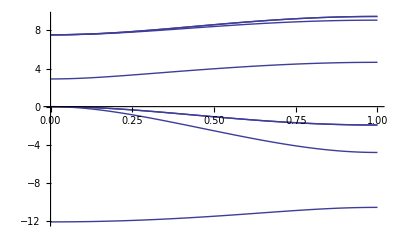

```mathematica
plot1=Plot[Sort[Eigenvalues[spMatrix/.{k1->x,k2->0,k3->0}]],{x,0,1}]
```

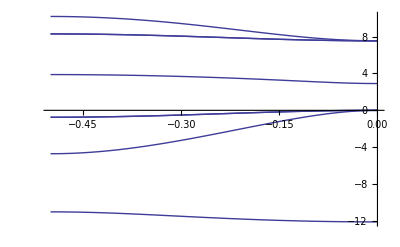

```mathematica
plot2=Plot[Sort[Eigenvalues[spMatrix/.{k1->x,k2->x,k3->x}]],{x,-0.5,0}]
```

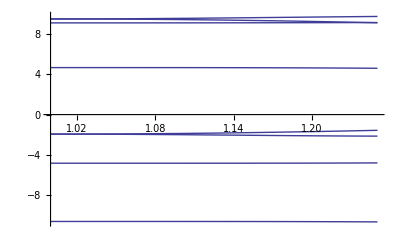

```mathematica
plot3=Plot[Sort[Eigenvalues[spMatrix/.{k1->1,k2->-(x-1),k3->x-1}]],{x,1,5/4}]
```

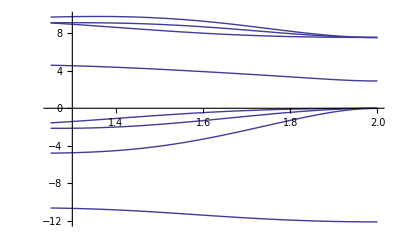

```mathematica
plot4=Plot[Sort[Eigenvalues[spMatrix/.{k1->3/4-(x-5/4),k2->-3/4+(x-5/4),k3->0}]],{x,5/4,2}]
```

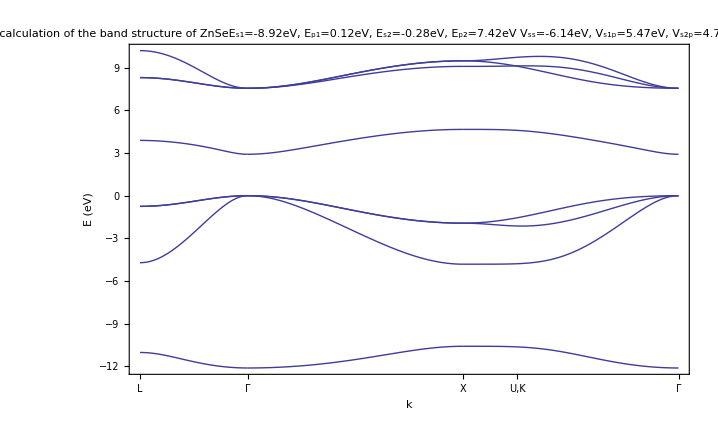

```mathematica
result=Show[plot1,plot2,plot3,plot4,
PlotRange->{{-0.5,2.0},All},Frame->True,
Axes->{True,False},
GridLines->{{-1/2,0,1,5/4,2},Automatic},
GridLinesStyle->{Directive[Thickness[0.001],Red],Gray},
FrameTicks->{{Automatic,Automatic},{{{-1/2,Style["L",FontSize->15]},{0,Style["Γ",FontSize->15]},{1,Style["X",FontSize->15]},{5/4,Style["U,K",FontSize->15]},{2,Style["Γ",FontSize->15]}},None}},
FrameLabel->{Style["k",FontSlant->Italic,FontWeight->Bold,FontSize->15],Style["E (eV)",FontSize->15,FontFamily->Times,FontSlant->Italic]},
PlotLabel->Row[{Style["Tight-binding calculation of the band structure of ZnSe",FontSize->25,FontFamily->Times],
Style["E_s1=-8.92eV, E_p1=0.12eV, E_s2=-0.28eV, E_p2=7.42eV\n V_ss=-6.14eV, V_s1p=5.47eV, V_s2p=4.73eV, V_xx=0.96eV, V_xy=4.38eV",FontSize->20,FontFamily->Times]},"\n"]]
```